```mathematica
(* Symmetry  l --> -l 
 H = l^2/2 detla{l' - l,0}  + (g2/2) (delta(l' - l,1) + delta(l' - l,-1))
*)
```

```mathematica
Clear[L]
diagonalK[L_]:=Table[l^2 /2 ,{l,-L, L }]
LzLz[L_] := DiagonalMatrix[diagonalK[L] ]
ident[L_] := IdentityMatrix[2 L +1] 
linkV[L_] := (2 ident[L] - DiagonalMatrix[Table[1,2L],1] - DiagonalMatrix[Table[1,2L],-1])/2
linkH[g_,L_]  := LzLz[L]+ (g^2/2)(2 ident[L] - DiagonalMatrix[Table[1,2L],1] - DiagonalMatrix[Table[1,2L],-1])
spareUpper[L_] :=  Table[If[i ==1&&j == 2L+1,1,0],{i,1,2L +1},{j,1,2 L+1}]
spareLower[L_] :=  Table[If[i ==2L +1&&j == 1,1,0],{i,1,2L +1},{j,1,2 L+1}]
clockH[g_,L_] := linkH[g,L]  -  (g^2/2)(spareUpper[L] + spareLower[L])
clockV[L_] := linkV[L]  -  (spareUpper[L] + spareLower[L])/2
harmonicH[x_,L_] :=  (1/x) LzLz[L]+x  linkV[L]  

linkHint[x_,L_]  := (1-x) LzLz[L]+ x (2 ident[L] - DiagonalMatrix[Table[1,2L],1] - DiagonalMatrix[Table[1,2L],-1])
clockHint[x_,L_] := linkHint[x,L]   -  x (spareUpper[L] + spareLower[L])
```

```mathematica
linkHint[x,4]
```

{{8 (1-x)+2 x,-x,0,0,0,0,0,0,0},{-x,(9 (1-x))/2+2 x,-x,0,0,0,0,0,0},{0,-x,2 (1-x)+2 x,-x,0,0,0,0,0},{0,0,-x,(1-x)/2+2 x,-x,0,0,0,0},{0,0,0,-x,2 x,-x,0,0,0},{0,0,0,0,-x,(1-x)/2+2 x,-x,0,0},{0,0,0,0,0,-x,2 (1-x)+2 x,-x,0},{0,0,0,0,0,0,-x,(9 (1-x))/2+2 x,-x},{0,0,0,0,0,0,0,-x,8 (1-x)+2 x}}

```mathematica
linkH[g,4]
```

{{8+g^2,-g^2/2,0,0,0,0,0,0,0},{-g^2/2,9/2+g^2,-g^2/2,0,0,0,0,0,0},{0,-g^2/2,2+g^2,-g^2/2,0,0,0,0,0},{0,0,-g^2/2,1/2+g^2,-g^2/2,0,0,0,0},{0,0,0,-g^2/2,g^2,-g^2/2,0,0,0},{0,0,0,0,-g^2/2,1/2+g^2,-g^2/2,0,0},{0,0,0,0,0,-g^2/2,2+g^2,-g^2/2,0},{0,0,0,0,0,0,-g^2/2,9/2+g^2,-g^2/2},{0,0,0,0,0,0,0,-g^2/2,8+g^2}}

```mathematica
Eigenvalues[linkH[2,4]]//N
```

{13.0235,13.0225,9.18064,9.02449,7.27701,6.11897,4.55111,2.83406,0.967731}

```mathematica
sortev = Sort[Eigenvalues[linkH[2,4]]//N]
```

{0.967731,2.83406,4.55111,6.11897,7.27701,9.02449,9.18064,13.0225,13.0235}

```mathematica
Take[sortev,3]
```

{0.967731,2.83406,4.55111}

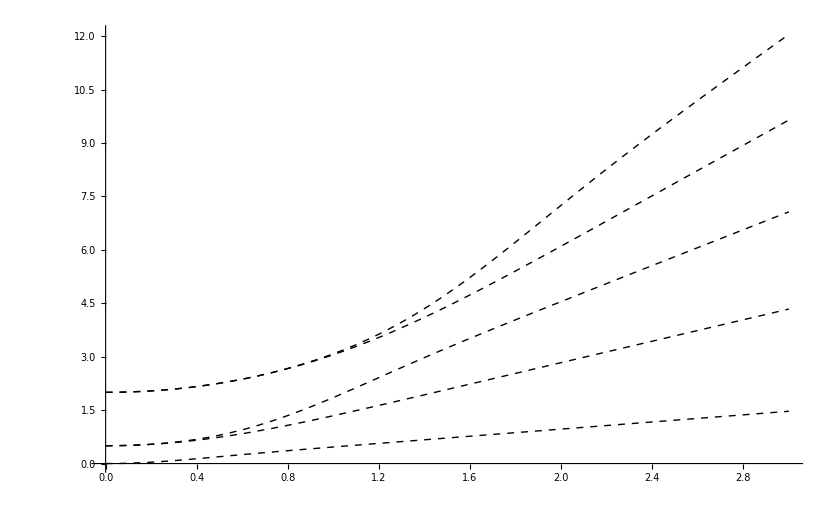

```mathematica
exactPlot = Plot[Take[Sort[Eigenvalues[linkH[g,64]]],5],{g,0,3},PlotStyle->{Black,Dashed,Thick}]
```

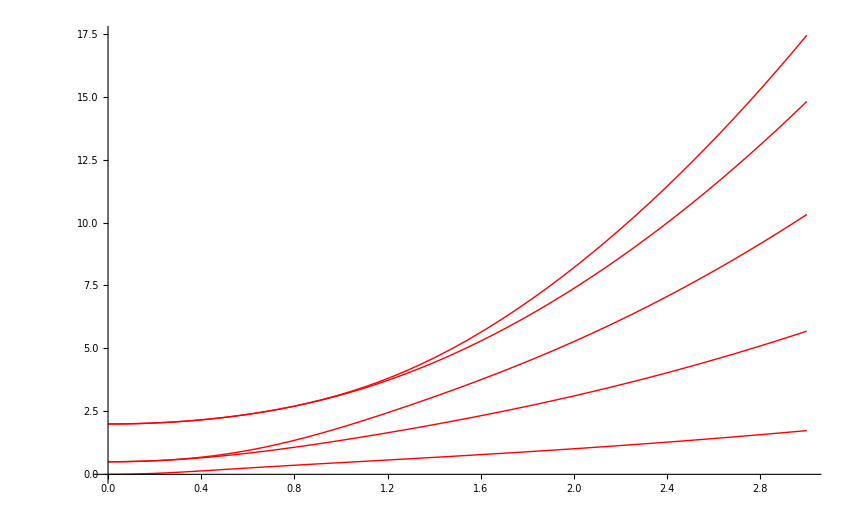

```mathematica
linkPlot = Plot[Take[Sort[Eigenvalues[linkH[g,2]]],5],{g,0,3},PlotStyle->{Red,Thick}]
```

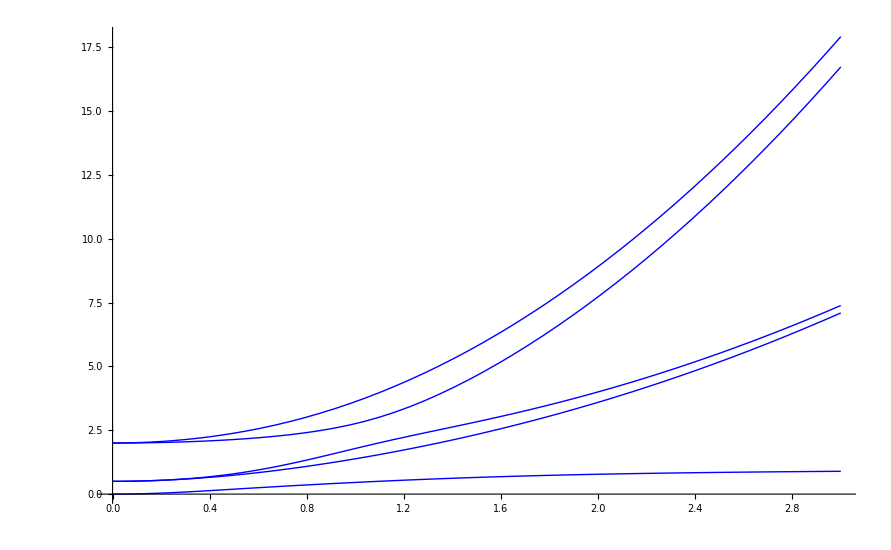

```mathematica
clockPlot= Plot[Take[Sort[Eigenvalues[clockH[g,2]]],5],{g,0,3},PlotStyle->{Blue,Thick}]
```

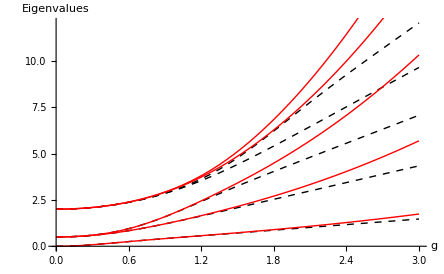

```mathematica
Show[exactPlot,linkPlot, AxesLabel->{"g", "Eigenvalues"}]
```

```mathematica
ExactSpec=Table[Take[Sort[Eigenvalues[linkH[g,32]]],5],{g,0,3, 0.01}];
LinkSpec=Table[Take[Sort[Eigenvalues[linkH[g,2]]],5],{g,0,3, 0.01}];
ClockSpec=Table[Take[Sort[Eigenvalues[clockH[g,2]]],5],{g,0,3, 0.01}];
```

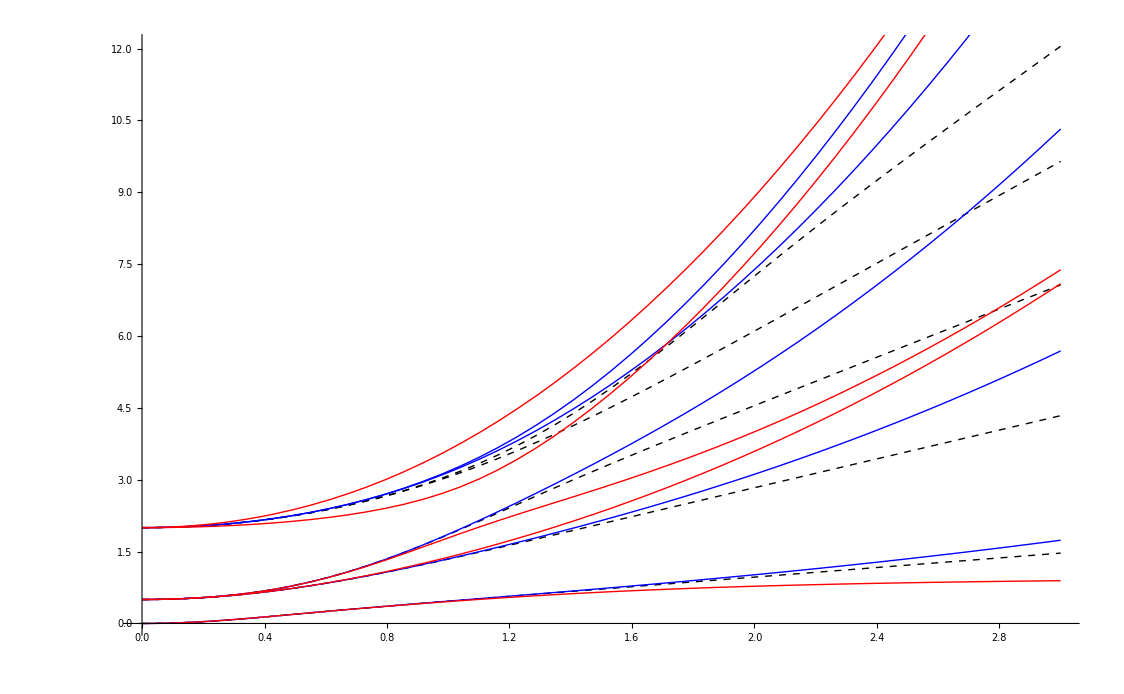

```mathematica
Show[exactPlot,linkPlot,clockPlot]
```

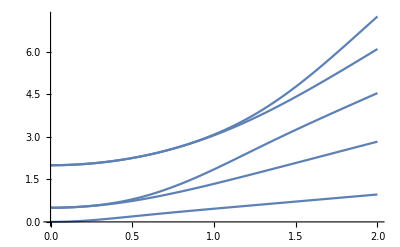

```mathematica
Plot[Take[Sort[Eigenvalues[linkH[g,32]]],5],{g,0,2}]
```

```mathematica
spareLow[L_] :=  Table[If[i ==1&&j == 2L+1,1,0],{i,1,2L +1},{j,1,2 L+1}]
```

```mathematica
spareLow[4]
```

{{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
Grid[%433]
```

Grid[%433]

```mathematica
Eigenvalues[linkV[4]] //N
```

{1.95106,1.80902,1.58779,1.30902,1.,0.690983,0.412215,0.190983,0.0489435}

```mathematica
Sort[{1.9510565162951536,1.8090169943749475,1.5877852522924731,1.3090169943749475,1.,0.6909830056250525,0.41221474770752686,0.19098300562505255,0.04894348370484647}]
```

{0.0489435,0.190983,0.412215,0.690983,1.,1.30902,1.58779,1.80902,1.95106}

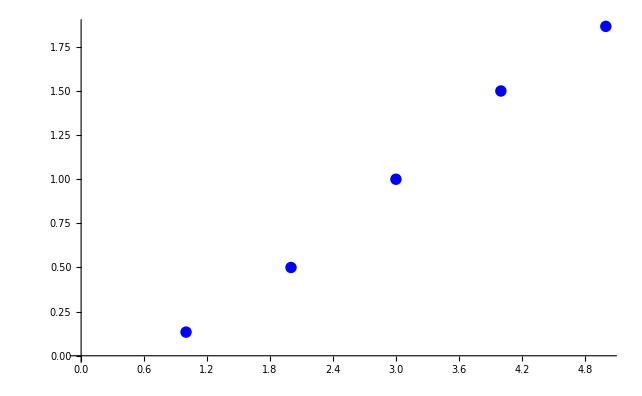

```mathematica
ListPlot[Sort[Eigenvalues[linkV[2]]//N],PlotStyle->{Blue}]
```

```mathematica
Sort[Eigenvalues[linkV[2]]//N]
```

{0.133975,0.5,1.,1.5,1.86603}

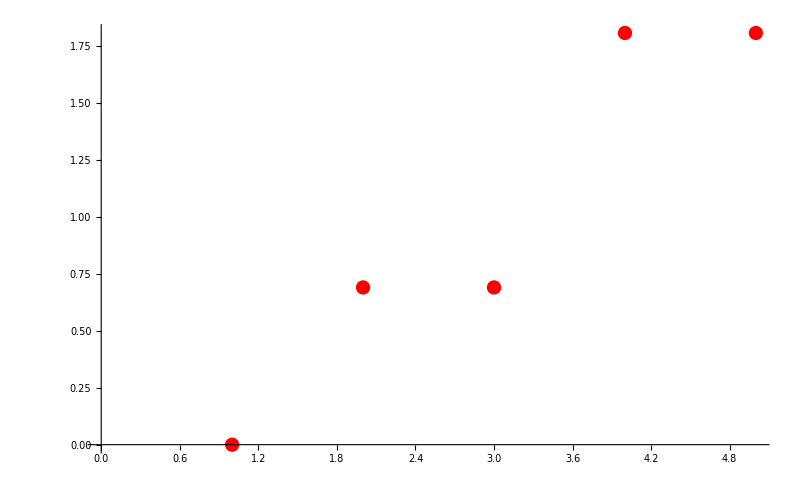

```mathematica
ListPlot[Sort[Eigenvalues[clockV[2]]//N],PlotStyle->{Red}]
```

```mathematica
Sort[Eigenvalues[clockV[2]]//N]
```

{0.,0.690983,0.690983,1.80902,1.80902}

{0.,0.690983,0.690983,1.80902,1.80902}

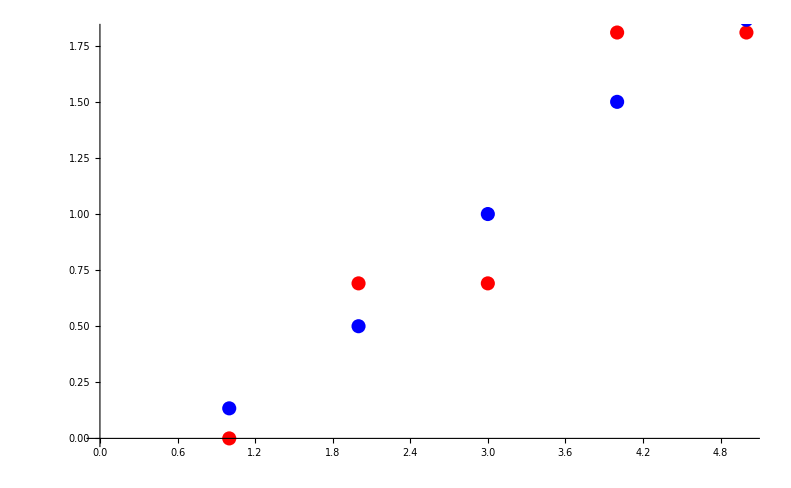

```mathematica
{0.,0.6909830056250525,0.6909830056250525,1.8090169943749475,1.8090169943749475}

Show[ ListPlot[Take[Sort[Eigenvalues[clockV[2]]//N],5],PlotStyle->{Red}],ListPlot[Take[Sort[Eigenvalues[linkV[2]]//N],5],PlotStyle->{Blue}]]
```

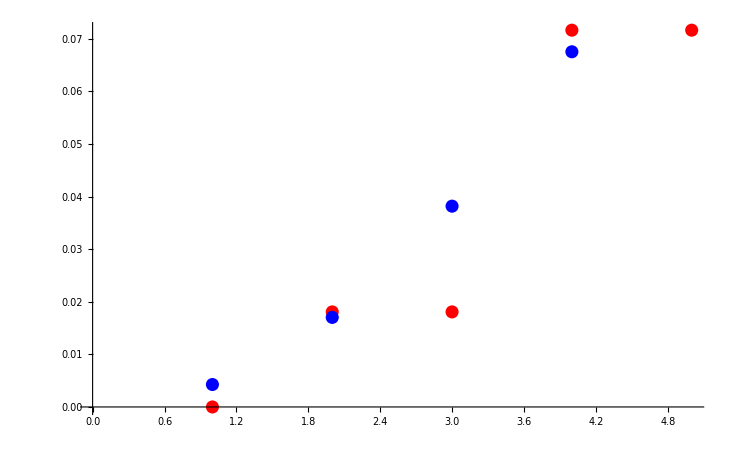

```mathematica
Show[ ListPlot[Take[Sort[Eigenvalues[clockV[16]]//N],5],PlotStyle->{Red}],ListPlot[Take[Sort[Eigenvalues[linkV[16]]//N],5],PlotStyle->{Blue}]]
```

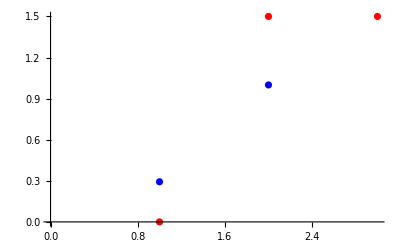

```mathematica
Show[ ListPlot[Sort[Eigenvalues[clockV[1]]//N],PlotStyle->{Red}],ListPlot[Sort[Eigenvalues[linkV[1]]//N],PlotStyle->{Blue}]]
```

```mathematica
Sort[Eigenvalues[linkHint[.25,2]]//N]
```

{0.277336,0.821946,1.04092,2.05305,2.05674}

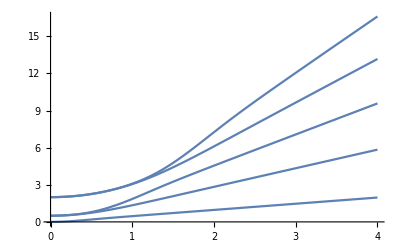

```mathematica
Plot[Take[Sort[Eigenvalues[linkH[g,16]]],5],{g,0,4}]
```

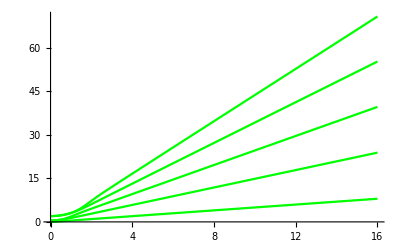

```mathematica
Plot[Take[Sort[Eigenvalues[linkH[g,16]]],5],{g,0,16},PlotStyle->{Green}]
```

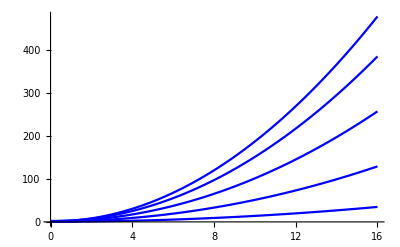

```mathematica
Plot[Sort[Eigenvalues[linkH[g,2]]],{g,0,16},PlotStyle->{Blue}]
```

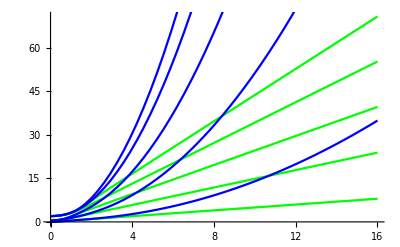

```mathematica
Show[{Plot[Take[Sort[Eigenvalues[linkH[g,16]]],5],{g,0,16},PlotStyle->{Green}],Plot[Sort[Eigenvalues[linkH[g,2]]],{g,0,16},PlotStyle->{Blue}]}]
```

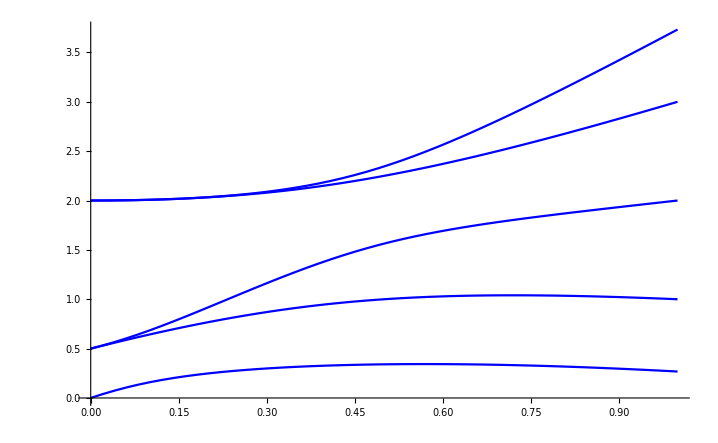

```mathematica
Plot[Sort[Eigenvalues[linkHint[x,2]]//N],{x,0,1},PlotStyle->{Blue}]
```

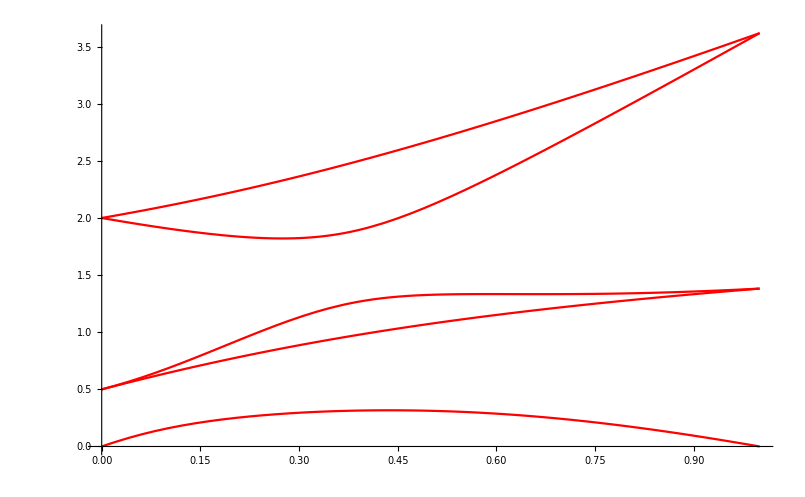

```mathematica
Plot[Sort[Eigenvalues[clockHint[x,2]]//N],{x,0,1},PlotStyle->{Red}]
```

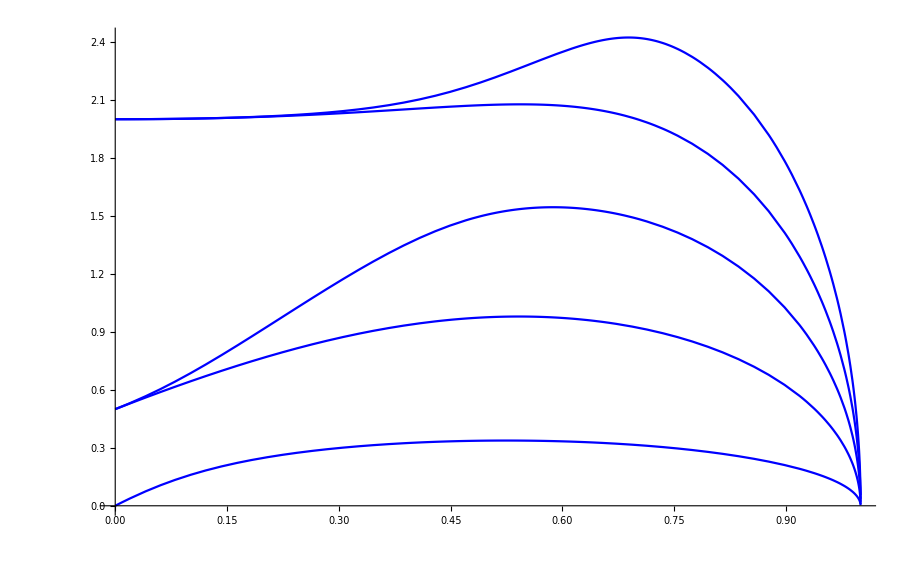

```mathematica
exactLinkInt= Plot[Take[Sort[Eigenvalues[linkHint[x,32]]//N],5],{x,0,1},PlotStyle->{Blue}]
```

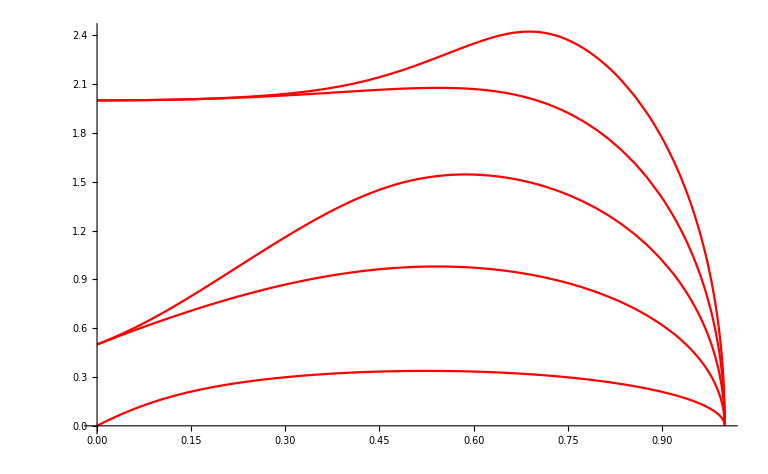

```mathematica
exactClockInt= Plot[Take[Sort[Eigenvalues[clockHint[x,32]]//N],5],{x,0,1},PlotStyle->{Red}]
```

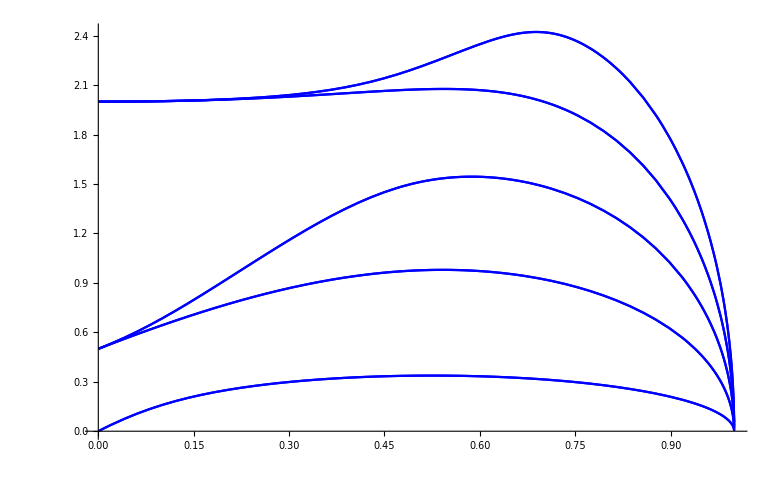

```mathematica
Show[{exactLinkInt,exactLinkInt}]
```

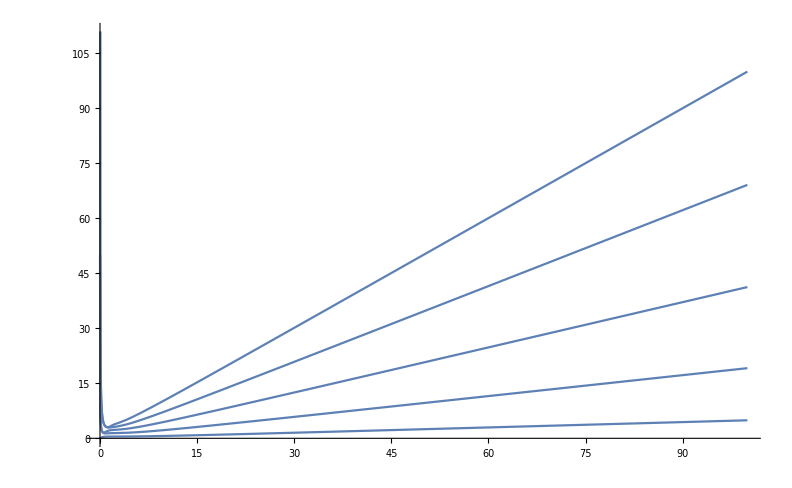

```mathematica
Plot[Take[Sort[Eigenvalues[harmonicH[x,4]]//N],5] ,{x,.01,100}]
```

```mathematica
Eigenvalues[harmonicH[1,2]]//N
```

{3.17323,3.15139,1.86112,1.34861,0.465646}